# DataRegion package

## by Ian Hinder

## Initialisation

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/barry/Research/Code/nrmma

```mathematica
<<"DataRegion.m"
```

```mathematica
<<CarpetHDF5`
```

## Documentation

The "DataRegion" Mathematica package provides a simple representation of a n-D block of numbers on a uniform Cartesian coordinate grid. The package uses an abstract type called "DataRegion" to represent each block.

A DataRegion object is printed in Mathematica as DataRegion[varName, dims, dataRange] to avoid printing large quantities of data.  To see the full structure, including all the data, use FullForm.

### ReadCarpetHDF5Variable[file, var, it, rl], ReadCarpetHDF5Variable[file, var, it, rl, map]

Note: The Carpet functions have been moved into a separate CarpetHDF5 package.

This function opens a set of Carpet HDF5 files and loads variable var, iteration it, refinement level rl, coordinate map map (if specified and using multipatch data), from the file set and returns it as a single DataRegion object.  It is currently assumed that the filename given, file, ends in either the suffix ".file_0.h5" (with a corresponding set of files ".file_<c>.h5"), or in ".x.<m>.h5", ".y.<m>.h5", ".z.<m>.h5", ".d.<m>.h5".  This set of files is opened, and component c is read from map m of each one.  The outermost cctk_nghostzones points are stripped from each component, and the components are then merged into a single DataRegion object.  If the components are disconnected, a single enclosing cuboid grid is created, and points which are not on any of the components are initialised to None.  In future, we could detect disconnected components and return a list of DataRegion objects for each one.

The metadata from HDF5 files is cached to improve performance. To clear the cache, see the ClearCarpetHDF5Cache[file] function.

For debugging, it can be helpful to know which parts of a HDF5 file are being read and when. Specifying the option VerboseRead->True, will make ReadCarpetHDF5[...] output verbose information about what it is doing.

### ClearCarpetHDF5Cache[file]

Note: The Carpet functions have been moved into a separate CarpetHDF5 package.

To improve performance, the ReadCarpetHDF5Variable[...] function caches some information (attributes, dataset names, dimensions) from the HDF5 file. Normally, this won't be a problem unless the contents of the HDF5 file change. If the file does change, run ClearCarpetHDF5Cache[...] to clear the cached data so that it will be read in again the next time ReadCarpetHDF5Var[...] is called.

### MakeDataRegion[data, name, dims, origin, spacing]

Manually create a DataRegion object from the list data. This data is assumed to be in column-major order, eg. data[[iz,iy,ix]] for the case of 3D data. The DataRegion will name the variable name, and assumes it has dimensions given by the list dims, with origing given by the list origin and spacing between points given by the list spacing.

### MergeDataRegions[{v1, v2, ...}]

Merge the DataRegions v1, v2, ... into a single enclosing data region.

### ReadVTKFile[file]

Note: The VTK functions have been moved into a separate CarpetVTK package.

Read the data file from file in VTK format and return it as a DataRegion object. file can either be a string, for a filename, or a stream object.  Currently there is very little error-checking, and strong assumptions are made about the format of the data.  It must be single-precision and in binary, not ascii, format.

### ToDataTable[v]

Convert a DataRegion to a DataTable object. This only works with 1D DataRegions for now.

### GetData[v]

Return a nested list, of depth equal to the dimensionality of the data containing the values from the DataRegion object v.  The data is ordered in column-major order (the same as Carpet), so when accessing points from the list, the array ordering is eg. data[[iz,iy,ix]] for the case of 3D data.  This means that, for example, extracting a slice of constant z-coordinate from 3D data is simple: data[[iz]].

### GetOrigin[v]

Return a list {o1, o2, o3, ...} containing the minimum x1, x2, x3,... coordinates of the block.

### GetSpacing[v]

Return a list {dx1, dx2, dx3, ...} containing the spacing between points in the x1, x2, x3, ... directions.

### GetDimensions[v]

Return a list {nx1, nx2, nx3, ...} containing the number of points in the x1, x2, x3, ... directions.

### GetNumDimensions[v]

Return an integer corresponding to the dimensionality of the data.

### GetDataRange[v]

Return a list of the form {{x1min, x1max}, {x2min, x2max}, {x3min, x3max}, ...} describing the minimum and maximum coordinates of the block.  This list can be used in the DataRange option of various Mathematica plotting functions.

### GetAttributes[v]

Return the list of attributes (Variable name, dimensions, origin, spacing, dimensionality) of the DataRegion.

### GetVariableName[v]

Return a string containing the variable name of the DataRegion v as recorded in the original file.

### Interpolation[v, ...]

The Interpolation function has been overloaded to work on DataRegion objects.  Internally, it uses ListInterpolation with the data and data ranges.  You can supply additional options for ListInterpolation to this function.  The resulting function will generically be a function of n variables, where n is the dimensionality of the data.  Interpolation might not work if the DataRegion contains data with value None, as will happen with Carpet data with disconnected components.

### SliceData[v, dim, coord:0]

Return a DataRegion object which is a slice through v in a plane perpendicular to dimension dim.  coord is the coordinate value at which to take the slice.  The resulting DataRegion object will have a dimensionality of 1 less than that of v.  To obtain the numerical data, use GetData on the resulting object.  For convenience, the coord argument can be omitted, defaulting to 0.0.

### DataRegionDensityPlot[v,...], DataRegionArayPlot[v,...], DataRegionPlot3D[v,...]

These are wrappers for the Mathematica 2D data plotting functions.  They operate on 2D DataRegion objects, automatically converting the object to a list and setting the data ranges appropriately.  You can use any plot arguments which are available in the corresponding regular Mathematica plotting function.

### DataRegionPlot[v,...]

These are wrappers for the Mathematica 1D data plotting functions.  They operate on 1D DataRegion objects, automatically converting the object to a list and setting the data ranges appropriately.  You can use any plot arguments which are available in the corresponding regular Mathematica plotting function.

### QuickSlicePlot[v, {min, max}, colorMap,...]

This provides a quick way to plot a 2D DataRegion.  It displays coordinates as well as a colormap key.  min and max correspond to the minimum and maximum values in the data to assign to 0 and 1 in the color map.  colorMap defaults to "TemperatureMap"; use ColorData["Gradients"] to get the list of possible color maps.

### Outline[v]

Produce a Graphics object (Line, Rectangle or Cuboid) with shape corresponding to that of the DataRegion.

## Notes

Interpolation on a DataRegion object with one of the dimensions small needs to be fixed.

## DataRegion Example

```mathematica
gxx=ReadCarpetHDF5Variable["sch_3c/output-0000/sch_3c/admbase::metric.file_0.h5","ADMBASE::gxx",0,0]
```

DataRegion[ADMBASE::gxx, {47, 47, 47}, {{-2.875, 2.875}, {-2.875, 2.875}, {-2.875, 2.875}}]

```mathematica
gxxSlice=SliceData[gxx,3]
```

DataRegion[ADMBASE::gxx, {47, 47}, {{-2.875, 2.875}, {-2.875, 2.875}}]

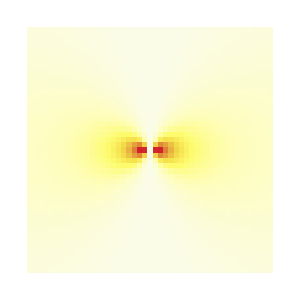

```mathematica
QuickSlicePlot[gxxSlice,{-1,1}]
```

(Note that the Cartesian components of g are not spherically symmetric.)

```mathematica
GetOrigin[gxx]
```

{-2.875,-2.875,-2.875}

```mathematica
GetSpacing[gxx]
```

{0.125,0.125,0.125}

```mathematica
GetDimensions[gxx]
```

{47,47,47}

```mathematica
{{xMin,xMax},{yMin,yMax},{zMin,zMax}}=GetDataRange[gxx]
```

{{-2.875,2.875},{-2.875,2.875},{-2.875,2.875}}

```mathematica
GetVariableName[gxx]
```

ADMBASE::gxx

```mathematica
gxxFn=Interpolation[gxx]
```

InterpolatingFunction[{{-2.875,2.875},{-2.875,2.875},{-2.875,2.875}},<>]

```mathematica
gxxFn[1.0,1.5,2.0]
```

1.10245

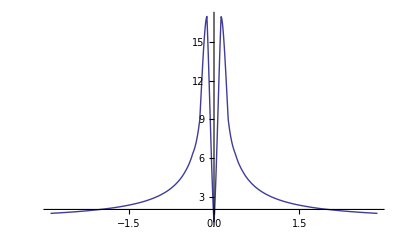

```mathematica
Plot[gxxFn[x,0,0],{x,xMin,xMax},PlotRange->All]
```

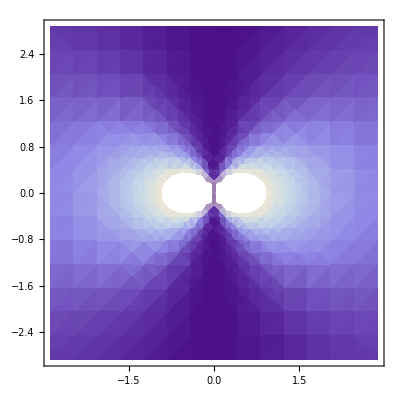

```mathematica
DensityPlot[gxxFn[x,y,0],{x,xMin,xMax},{y,yMin,yMax}]
```